```mathematica
d=1;
q=0.6;
M=7.452486380456643;
```

```mathematica
dS1[t_] =   Cross[1/(2 d^3)((4+3q)(J[t]-S1[t]-S2[t])-(3q)/(q+1)((1+q)Dot[S1[t],J[t]-S1[t]-S2[t]]+(1+1/q)Dot[S2[t],J[t]-S1[t]-S2[t]]) (J[t]-S1[t]-S2[t])/Norm[J[t]-S1[t]-S2[t]]^2  + S2[t]   )  ,S1[t]];
dS2[t_] =    Cross[1/(2 d^3)((4+3/q)(J[t]-S1[t]-S2[t])-3/(q+1)((1+q)Dot[S1[t],J[t]-S1[t]-S2[t]]+(1+1/q)Dot[S2[t],J[t]-S1[t]-S2[t]]) (J[t]-S1[t]-S2[t])/Norm[J[t]-S1[t]-S2[t]]^2    + S1[t]    ) ,S2[t]];
dJ[t_]=     {0,0,0}  ;
```

```mathematica
S10={-3,-6,-1};
S20={-4,-6,-3};
J0={0,0,12};
S0=S10+S20;
L0=J0-S0;

(*ξmin*)
S11={-4.114462718048539,-5.129059112271103,-1.6625129066017452};
S21={-2.885537281951461,-6.870940887728898,-2.337487093398255};
J1=J0;
Sv1=S11+S21;
Lv1=J1-Sv1;

S12={-4.08942794234023,-5.204077375291083,-1.4812689750313446};
S22={-2.9105720576597687,-6.795922624708916,-2.518731024968656};
J2=J0;
Sv2=S12+S22;
Lv2=J2-Sv2;

{Norm[S10]==Norm[S11]==Norm[S12],Norm[S20]==Norm[S21]==Norm[S22],Norm[L0]==Norm[Lv1]==Norm[Lv2],Norm[S0]==Norm[Sv1]==Norm[Sv2],Norm[J0]==Norm[J1]==Norm[J2]}
```

{True,True,True,True,True}

```mathematica
sol0=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]==S10,S2[0]==S20, J[0]==J0  },   {S1,S2,J},{t,0,30}];
sol1=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]==S11,S2[0]==S21, J[0]==J1  },   {S1,S2,J},{t,0,30}];
sol2=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]==S12,S2[0]==S22, J[0]==J2  },   {S1,S2,J},{t,0,30}];
```

```mathematica
ξ0=1/M^2 Dot[((1+q)S10+(1+1/q)S20),L0/Norm[L0]];
ξ1=1/M^2 Dot[((1+q)S11+(1+1/q)S21),Lv1/Norm[Lv1]];
ξ2=1/M^2 Dot[((1+q)S12+(1+1/q)S22),Lv2/Norm[Lv2]];
{ξ0,ξ1,ξ2}
```

{-0.483546,-0.47634,-0.478311}

```mathematica
normrules={J->Norm[J0],L->Norm[L0],S1->Norm[S10],S2->Norm[S20]}//N
```

{J→12.,L→21.1896,S1→6.78233,S2→7.81025}

```mathematica
J>S1+S2-L//.normrules
Smin=Max[Abs[J-L],Abs[S1-S2]]//.normrules
Smax=Min[J+L,S1+S2]//.normrules
```

True

9.18962

14.5926

```mathematica
ξmax=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.S->Smin
ξmin=1/(4 L M^2  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.S->Smax
```

-0.368657

-0.477713

```mathematica
NormS0[t_]:=Norm[(S1/.sol0[[1]])[t]+(S2/.sol0[[1]])[t]];
NormS1[t_]:=Norm[(S1/.sol1[[1]])[t]+(S2/.sol1[[1]])[t]];
NormS2[t_]:=Norm[(S1/.sol2[[1]])[t]+(S2/.sol2[[1]])[t]]
```

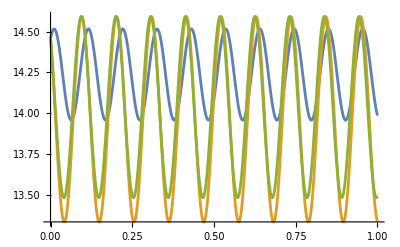

```mathematica
Plot[{NormS0[t],NormS1[t],NormS2[t]},{t,0,1}]
```

```mathematica
ContξSp=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.Cos[ϕ]->-1//FullSimplify;
ContξSm=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.Cos[ϕ]->+1//FullSimplify;
```

```mathematica
TheEgg=RegionPlot[{ξ>ContξSm&&ξ<ContξSp&&ξ<ξmax,ξ>ContξSm&&ξ<ContξSp&&ξ>ξmax,ξ>ContξSm&&ξ<ContξSp&&ξmin<ξ<ξmax},{S,Smin,Smax},{ξ,ξmin-0.1,ξmax+0.1},PlotRange->{All,All},ImageSize->Large];
```

```mathematica
Manipulate[Show[TheEgg,Graphics[{PointSize[0.015],Black,Point[{NormS0[t],ξ0}]}],Graphics[{PointSize[0.015],Purple,Point[{NormS1[t],ξ1}]}],Graphics[{PointSize[0.015],Blue,Point[{NormS2[t],ξ2}]}],PlotRange->All,Frame->True,FrameLabel->{Style["S(t)",15,Black],Style["ξ",15,Black]},FrameStyle->Directive[15,Black]],{t,0,0.5}]
```

```mathematica
S1V1[t_]:=(S1/.sol1[[1]])[t]
S2V1[t_]:=(S2/.sol1[[1]])[t]
JV1[t_]:=(J/.sol1[[1]])[t]
LV1[t_]:=JV1[t]-S1V1[t]-S2V1[t]
SV1[t_]:=S1V1[t]+S2V1[t]
```

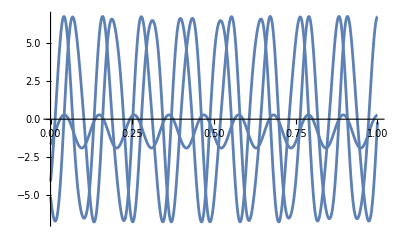
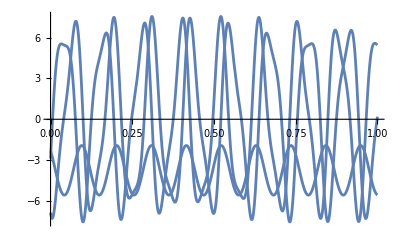
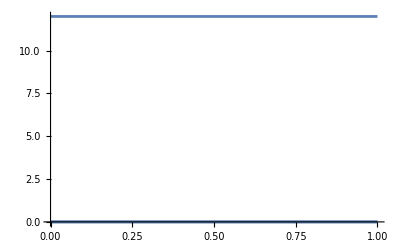
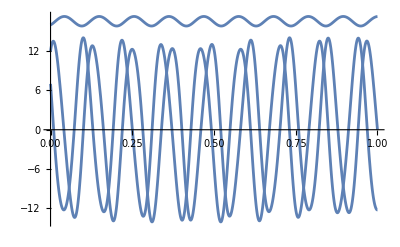

```mathematica
{Plot[S1V1[t],{t,0,1}],Plot[S2V1[t],{t,0,1}],Plot[JV1[t],{t,0,1}],Plot[LV1[t],{t,0,1}]}
```

```mathematica
S1V2[t_]:=(S1/.sol2[[1]])[t]
S2V2[t_]:=(S2/.sol2[[1]])[t]
JV2[t_]:=(J/.sol2[[1]])[t]
LV2[t_]:=JV2[t]-S1V2[t]-S2V2[t]
SV2[t_]:=S1V2[t]+S2V2[t]
```

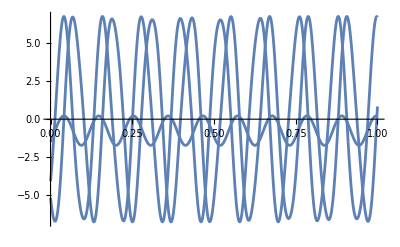
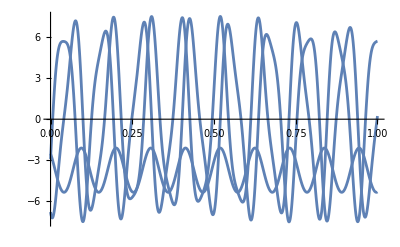
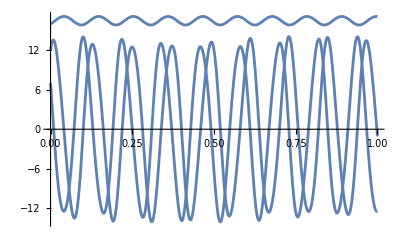
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[S1V2[t],{t,0,1}],Plot[S2V2[t],{t,0,1}],Plot[JV2[t],{t,0,1}],Plot[LV2[t],{t,0,1}]}
```

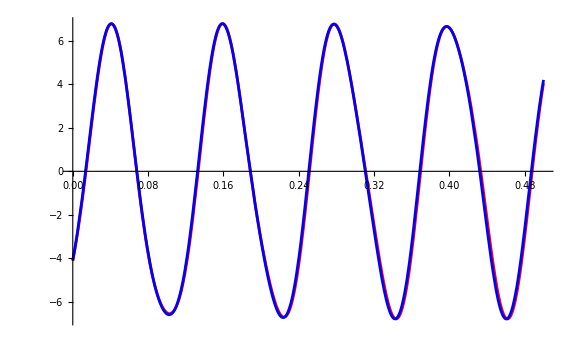

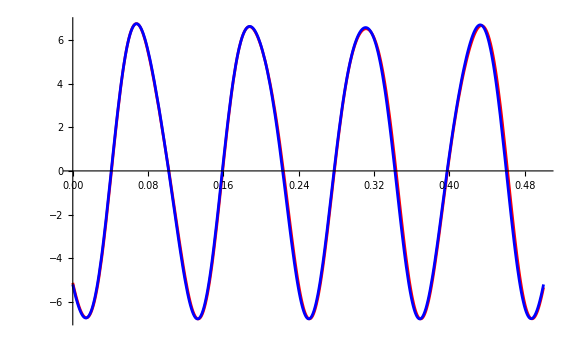

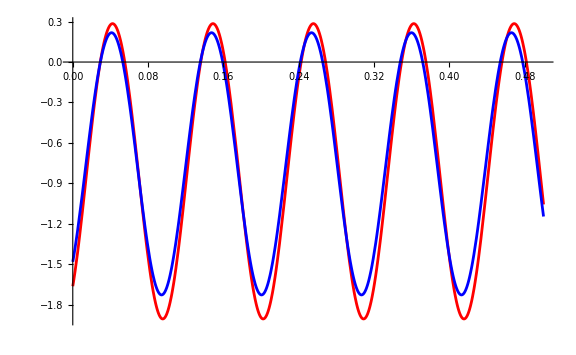

```mathematica
(*Test for S1 vector components*)
Plot[{S1V1[t][[1]],S1V2[t][[1]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
Plot[{S1V1[t][[2]],S1V2[t][[2]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
Plot[{S1V1[t][[3]],S1V2[t][[3]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
```

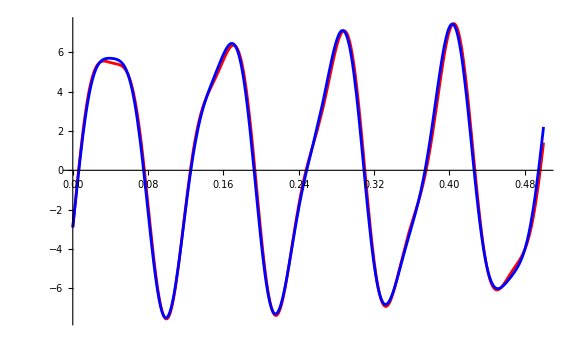

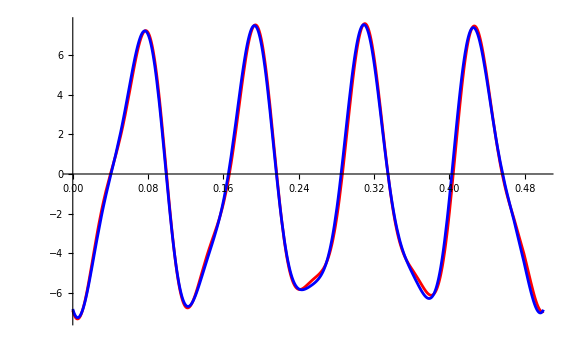

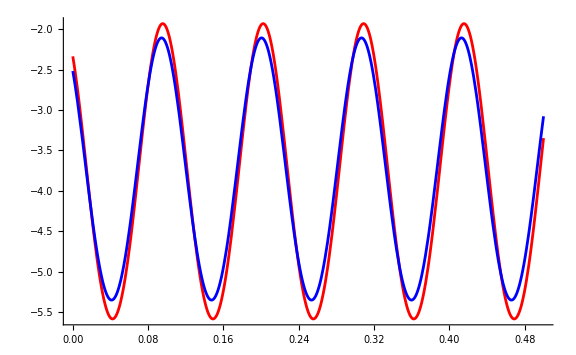

```mathematica
(*Test for S2 vector components*)
Plot[{S2V1[t][[1]],S2V2[t][[1]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
Plot[{S2V1[t][[2]],S2V2[t][[2]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
Plot[{S2V1[t][[3]],S2V2[t][[3]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
```

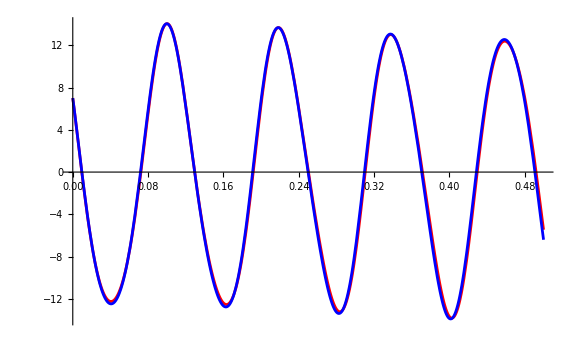

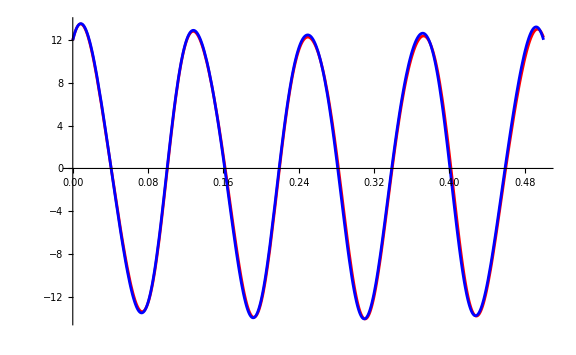

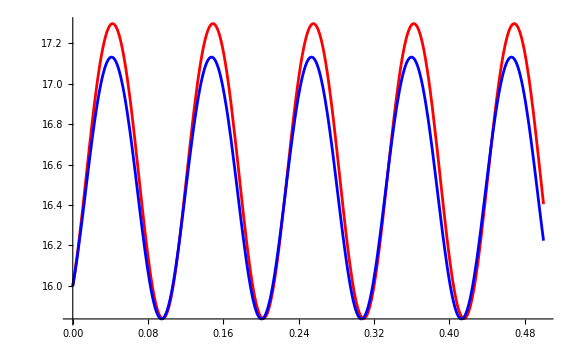

```mathematica
(*Test for L vector components*)
Plot[{LV1[t][[1]],LV2[t][[1]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
Plot[{LV1[t][[2]],LV2[t][[2]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
Plot[{LV1[t][[3]],LV2[t][[3]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
```

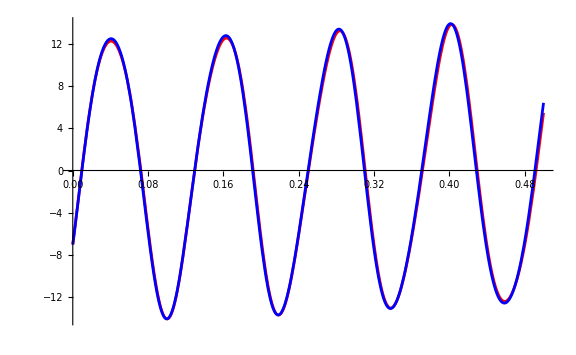

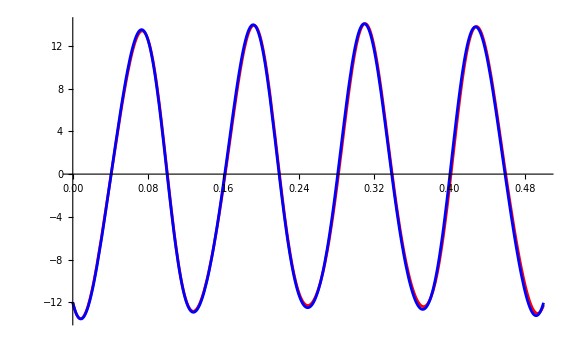

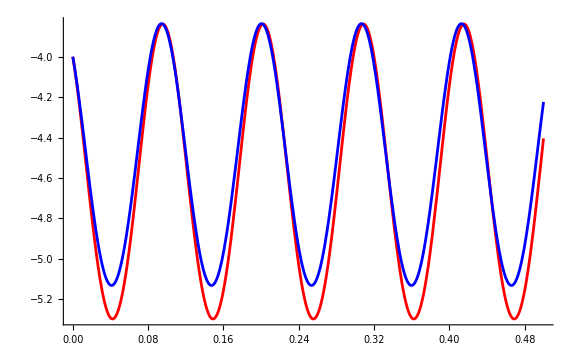

```mathematica
(*Test for S vector components*)
Plot[{SV1[t][[1]],SV2[t][[1]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
Plot[{SV1[t][[2]],SV2[t][[2]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
Plot[{SV1[t][[3]],SV2[t][[3]]},{t,0,0.5},PlotStyle->{Red,Blue},AxesLabel->{Style["",16],Style["",16]},ImageSize->Large]
```

```mathematica
A1=(J^2-(L-S)^2)^(1/2);
A2=((L+S)^2-J^2)^(1/2);
A3=(S^2-(S1-S2)^2)^(1/2);
A4=((S1+S2)^2-S^2)^(1/2);
```

```mathematica
Simplify[((J^2-L^2-S^2)(S^2(1+q)^2-(S1^2-S2^2)(1-q^2))-(1-q^2)A1 A2 A3 A4 Cos[ϕ])/(4q M^2 S^2 L)/.S1->Norm[S10]/.S2->Norm[S20]/.L->Norm[L0]/.J->Norm[J0]]
```

(-1.03666-0.27984 S^2-0.000906365 S^4-0.000226591 √(-305+2 √449 S-S^2) √(305+2 √449 S+S^2) √(-225+214 S^2-S^4) Cos[ϕ])/S^2

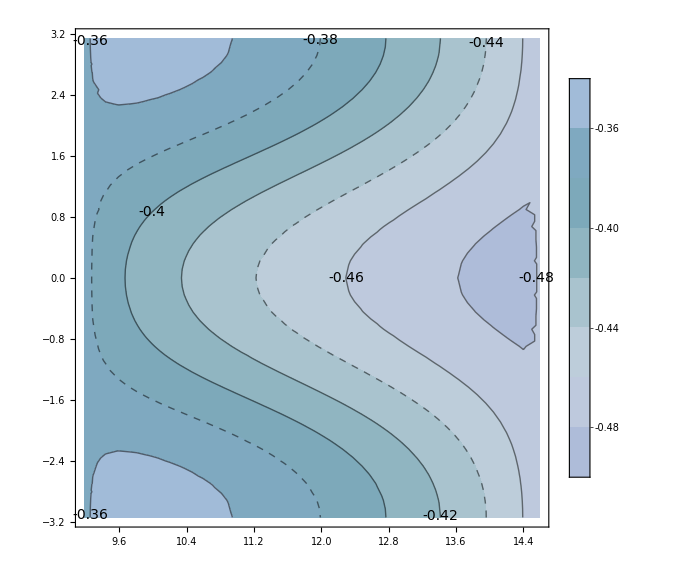

```mathematica
ContourPlot[(-1.0366550749560202-0.27984022241982187 S^2-0.0009063650928577227 S^4-0.00022659127321443063 √(-305+2 √449 S-S^2) √(305+2 √449 S+S^2) √(-225+214 S^2-S^4) Cos[ϕ])/S^2,{S,Smin,Smax},{ϕ,-π,π},FrameLabel->{Style["",16],Style["",16]},ContourLabels->(Text[Style[#3,14],{#1,#2},Background->LightYellow]&),PlotLegends->Automatic,ColorFunction->"Aquamarine",ContourStyle->{Black,Black,Dashed},ImageSize->Large]
```

#### Mass parameters calculations

```mathematica
Norm[S10]//N
```

6.78233

```mathematica
Norm[S20]//N
```

7.81025

```mathematica
mass2=Solve[m2^2==Norm[S20],m2][[2]]//N
```

{m2→2.79468}

```mathematica
masstotal=Solve[m2==(q MM)/(q+1),MM][[1]]/.mass2
```

{MM→7.45249}

```mathematica
mass1=Solve[m1+m2==MM,m1][[1]]/.masstotal/.mass2
```

{m1→4.6578}

```mathematica
chi1=Solve[Norm[S10]==x1 m1^2,x1][[1]]/.mass1
```

{x1→0.31262}

```mathematica
{m2/m1 }/.mass2/.mass1
```

{0.6}

```mathematica
{m2<m1 }/.mass2/.mass1
```

{True}

```mathematica
Norm[S20]>Norm[S10]
```

True

```mathematica
{m1^2 x1<m2^2 x2}/.chi1/.x2->1/.mass1/.mass2
```

{True}

```mathematica
eta={η->(m1 m2)/MM^2}/.masstotal/.mass1/.mass2
```

{η→0.234375}

```mathematica
distance=Solve[Norm[L0]==η(r MM^3)^(1/2),r]/.masstotal
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→1.08478/η^2}}

```mathematica
Norm[S10]+Norm[S20]==Smax
```

True

```mathematica
Norm[J0]>Abs[Norm[L0]-Norm[S10]-Norm[S20]]
```

True

```mathematica
Max[0,Norm[L0]-Norm[S10]-Norm[S20],Abs[Norm[S10]-Norm[S20]]-Norm[L0]]//N
```

6.59704

```mathematica
Norm[L0]+Norm[S10]+Norm[S20]//N
```

35.7822

```mathematica
Norm[L0]>Norm[S10]+Norm[S20]
```

True

#### Angle behavior

```mathematica
S1V0[t_]:=(S1/.sol0[[1]])[t]
S2V0[t_]:=(S2/.sol0[[1]])[t]
JV0[t_]:=(J/.sol0[[1]])[t]
LV0[t_]:=JV0[t]-S1V0[t]-S2V0[t]
SV0[t_]:=S1V0[t]+S2V0[t]
```

```mathematica
S1u1[t_]:=S1V1[t]/Norm[S1V1[t]];
S1u2[t_]:=S1V2[t]/Norm[S1V2[t]];
Su1[t_]:=SV1[t]/Norm[SV1[t]];
Su2[t_]:=SV2[t]/Norm[SV2[t]];
```

```mathematica
zcapZ[t_]:=JV0[t]/(JV0[t][[3]])
xcapX[t_]:=(LV0[t]-(Dot[LV0[t],zcapZ[t]]zcapZ[t]))/Norm[LV0[t]-(Dot[LV0[t],zcapZ[t]]zcapZ[t])]
ycapY[t_]:=Cross[zcapZ[t],xcapX[t]]
```

```mathematica
SO11[t_]:=Cross[ycapY[t],SV1[t]];
SO12[t_]:=Cross[ycapY[t],SV2[t]];
SOu1[t_]:=SO11[t]/Norm[SO11[t]];
SOu2[t_]:=SO12[t]/Norm[SO12[t]];
```

```mathematica
cosϕ11[t_]:=Dot[S1u1[t],SOu1[t]]/Norm[Cross[S1u1[t],Su1[t]]];
cosϕ12[t_]:=Dot[S1u2[t],SOu2[t]]/Norm[Cross[S1u2[t],Su2[t]]];
```

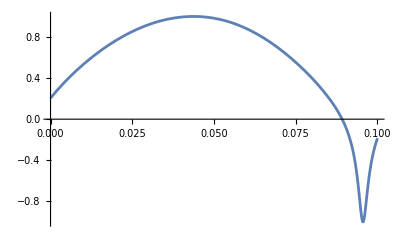

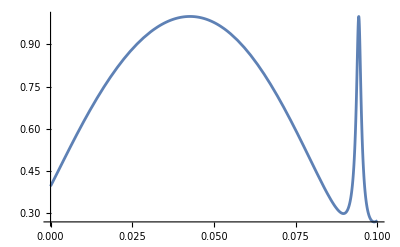

```mathematica
Plot[cosϕ11[t],{t,0,0.1}]
Plot[cosϕ12[t],{t,0,0.1}]
```